# Mathematica learning note

## Basics

```mathematica
l1=List[0,1,0]   (*Lists*)
```

{0,1,0}

```mathematica
l2=(l1+Range[1,12,4]^2*2)*{1,2,3}  (*List arithmetics*)
```

{2,102,486}

```mathematica
l3=Sort[Join[l1,Reverse[l2]]-2]  (*List operations*)
```

{-2,-2,-1,0,100,484}

```mathematica
{-2,-2,-1,0,16,52}
```

```mathematica
Max[l3]==l3[[-1]] && Min[l3]==l3[[1]]
```

True

```mathematica
Take[Drop[IntegerDigits[2^10],1],2]  (*List manipulations*)
```

{0,2}

```mathematica
Total[n=Range[100]]==1/2*Length[n](First[n]+Last[n])   (*Arithmetic series*)
```

True

```mathematica
Total[Table[3^k,{k,0,10}]]==(1-r^(n+1))/(1-r)/.{r->3,n->10}  (*Geometric series*)
```

True

```mathematica
sentence="A sentence."
```

A sentence.

```mathematica
StringLength[StringReverse[sentence]]==Length[Characters[sentence]]
```

True

```mathematica
LetterCounts[StringJoin[words=WordList[]],IgnoreCase->True]  (*Compute letter frequencies*)
```

<|e→37643,i→29235,a→26357,n→24296,r→24012,t→23681,o→21499,s→21462,l→19752,c→14572,u→12319,d→11779,p→9891,m→9384,g→8696,h→7728,y→7567,b→6668,f→4967,v→3718,w→2878,k→2772,z→1117,x→980,q→630,j→546|>

## Graphics and Plots

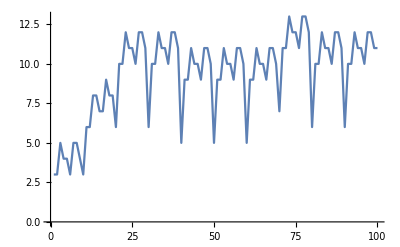
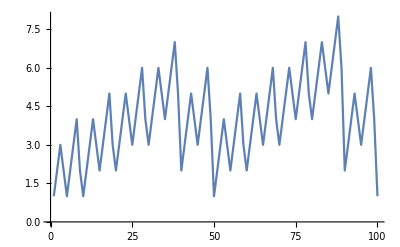

```mathematica
Row[{ListLinePlot[Table[StringLength[IntegerName[n]],{n,100}]],ListLinePlot[Table[StringLength[RomanNumeral[n]],{n,100}]]}](*Length of the Roman numerals and Names*)
```

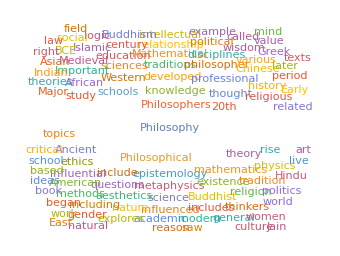

```mathematica
WordCloud[WikipediaData["Philosophy"]]  (*WordCloud & Wikipedia*)
```

```mathematica
Blend[{ColorNegate[Yellow],Yellow}]==RGBColor[0.5,0.5,0.5]  (*Colour mixing*)
```

True

```mathematica
Grid[Table[RGBColor[r,0,b],{r,0,1,.2},{b,0,1,.2}]]  (*Gradual spectrum*)
```

RGBColor[0., 0, 0.] | RGBColor[0., 0, 0.2] | RGBColor[0., 0, 0.4] | RGBColor[0., 0, 0.6000000000000001] | RGBColor[0., 0, 0.8] | RGBColor[0., 0, 1.]
RGBColor[0.2, 0, 0.] | RGBColor[0.2, 0, 0.2] | RGBColor[0.2, 0, 0.4] | RGBColor[0.2, 0, 0.6000000000000001] | RGBColor[0.2, 0, 0.8] | RGBColor[0.2, 0, 1.]
RGBColor[0.4, 0, 0.] | RGBColor[0.4, 0, 0.2] | RGBColor[0.4, 0, 0.4] | RGBColor[0.4, 0, 0.6000000000000001] | RGBColor[0.4, 0, 0.8] | RGBColor[0.4, 0, 1.]
RGBColor[0.6000000000000001, 0, 0.] | RGBColor[0.6000000000000001, 0, 0.2] | RGBColor[0.6000000000000001, 0, 0.4] | RGBColor[0.6000000000000001, 0, 0.6000000000000001] | RGBColor[0.6000000000000001, 0, 0.8] | RGBColor[0.6000000000000001, 0, 1.]
RGBColor[0.8, 0, 0.] | RGBColor[0.8, 0, 0.2] | RGBColor[0.8, 0, 0.4] | RGBColor[0.8, 0, 0.6000000000000001] | RGBColor[0.8, 0, 0.8] | RGBColor[0.8, 0, 1.]
RGBColor[1., 0, 0.] | RGBColor[1., 0, 0.2] | RGBColor[1., 0, 0.4] | RGBColor[1., 0, 0.6000000000000001] | RGBColor[1., 0, 0.8] | RGBColor[1., 0, 1.]

```mathematica
Table[Hue[x],{x,0,1,0.05}]  (*Gradual hue*)
```

{Hue[0.],Hue[0.05],Hue[0.1],Hue[0.15000000000000002],Hue[0.2],Hue[0.25],Hue[0.30000000000000004],Hue[0.35000000000000003],Hue[0.4],Hue[0.45],Hue[0.5],Hue[0.55],Hue[0.6000000000000001],Hue[0.65],Hue[0.7000000000000001],Hue[0.75],Hue[0.8],Hue[0.8500000000000001],Hue[0.9],Hue[0.9500000000000001],Hue[1.]}

```mathematica
Table[Style[RandomInteger[9],RandomColor[],n],{n,30}]  (*Font styles*)
```

{0,5,1,7,2,9,8,9,0,2,6,2,1,4,3,9,4,2,5,0,6,5,0,9,2,5,5,0,8,8}

```mathematica
wa=Transliterate[StringReplace["Wolfram|Alpha","ph"->"f"],"Cyrillic"]  (*Transliteration*)
```

Уолфрам|Алфа

```mathematica
ArrayPlot[1-ImageData[Binarize[Rasterize[wa]]]]
```

-Graphics-

```mathematica
Manipulate[Graphics[Style[RegularPolygon[n],Hue[h]],ImageSize->s],{n,Range[5,10]},{h,0,1}, {s,{Tiny,Small}}]  (*Interactive & Polygons*)
```

```mathematica
Graphics3D[Table[Style[Sphere[RandomInteger[10,3]],Opacity[0.5]],50]]
```

-Graphics3D-

```mathematica
CurrentImage[]  (*Get image from camera*)
```

```mathematica
ImageCollage[Table[Blur[ColorNegate[-Graphics-],n],{n,0,15,5}]]  (*Operations on image*)
```

-Graphics-

```mathematica
ImageAdd[im=-Graphics-,EdgeDetect[im]]  (*Edge-detection*)
```

-Graphics-

```mathematica
GraphicsGrid[Partition[Table[ArrayPlot[CellularAutomaton[n,{{1},0},{40,All}]],{n,0,255}],16]]  (*Cellular Automaton*)
```

-Graphics-